```mathematica
data={{20,0.99},{36,0.998},{50,0.9995}}
fit=Fit[data,{1,x,x^2,x^3},x]
```

{{20,0.99},{36,0.998},{50,0.9995}}

0.95409+0.00284489 x-0.000061625 x^2+4.57828×10^-7 x^3

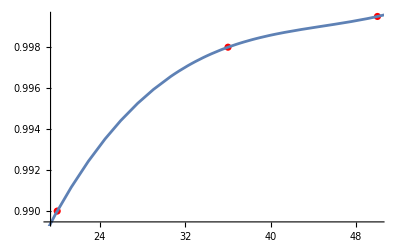

At x=20: 0.99

At x=36: 0.998

At x=50: 0.9995

```mathematica
Show[ListPlot[data,PlotStyle->Red],Plot[fit,{x, 0, 75}]]
Print["At x=20: ",fit/. x->20];
Print["At x=36: ",fit/. x->36];
Print["At x=50: ",fit/. x->50];
```